```mathematica
(*SetOptions[ListPlot,{PlotRange->{ 2 10^-4,10^-3}}];*)
```

```mathematica
path="/home/mashry/hep/SSP-1.2.5/Output/";
Get[path<>"plot.m"]
st[x_]:=ToString[x];
ex[x_]:=ToExpression[x];
dat1={"TanBeta","gBL","gYB","mC12","mC22","x1","x2","hh_2","M1","M2","M3","HB Result (1: allowed, 0: excluded, -1: unphysical)","HS total Chi^2","xsection"};
dat2={"dh_2","mh_2"};
prcs={"pphhaabb","ppzz4l"};
prcs1={"pphhaabb"};
prcs2={"ppzz4l"};
prcs=prcs;
Do[ex[prcs[[i]]<>dat1[[j]]]=Import[path<>prcs[[i]]<>"_"<>dat1[[j]]<>".dat"];,{i,Length[prcs]},{j,Length[dat1]}];
Do[ex["l1"<>prcs[[i]]<>dat1[[j]]]=Length[ex[prcs[[i]]<>dat1[[j]]]];,{i,Length[prcs]},{j,Length[dat1]}];
Do[ex["l2"<>prcs[[i]]<>dat1[[j]]]=Length[ex[prcs[[i]]<>dat1[[j]]][[1]]];,{i,Length[prcs]},{j,Length[dat1]}];
Do[Export[path<>prcs[[j]]<>"_dh_2.dat",Table[ex[prcs[[j]]<>"hh_2"][[2i]],{i,Ceiling[Length[ex[prcs[[j]]<>"hh_2"]]/2]}]]&&Export[path<>prcs[[j]]<>"_mh_2.dat",Table[ex[prcs[[j]]<>"hh_2"][[2i-1]],{i,Ceiling[Length[ex[prcs[[j]]<>"hh_2"]]/2]}]];,{j,Length[prcs]}];
```

```mathematica
Do[ex[prcs[[i]]<>dat2[[j]]]=Import[path<>prcs[[i]]<>"_"<>dat2[[j]]<>".dat"];,{i,Length[prcs]},{j,Length[dat2]}];
Do[ex["l1"<>prcs[[i]]<>dat2[[j]]]=Length[ex[prcs[[i]]<>dat2[[j]]]];,{i,Length[prcs]},{j,Length[dat2]}];
Do[ex["l2"<>prcs[[i]]<>dat2[[j]]]=Length[ex[prcs[[i]]<>dat2[[j]]][[1]]];,{i,Length[prcs]},{j,Length[dat2]}];
SetOptions[ListPlot,PlotRange->{0.0003,0.0004}];
```

```mathematica
lstplt[i1_,j1_,i2_,j2_]:=ListPlot[Table[{ex[prcs[[i1]]<>dat1[[j1]]][[k,Length[ex[prcs[[i1]]<>dat1[[j1]]][[1]]]]],ex[prcs[[i2]]<>dat1[[j2]]][[k,Length[ex[prcs[[i2]]<>dat1[[j2]]][[1]]]]]},{k,Length[ex[prcs[[i1]]<>dat1[[j1]]]]}],FrameLabel->{prcs[[i1]]<>dat1[[j1]],prcs[[i2]]<>dat1[[j2]]}]
(*Do[Print[lstplt[i1,j1,i2,j2]],{i1,Length[prcs]},{j1,Length[dat1]},{i2,Length[prcs]},{j2,j1+1,2+0Length[dat1]}]*)
```

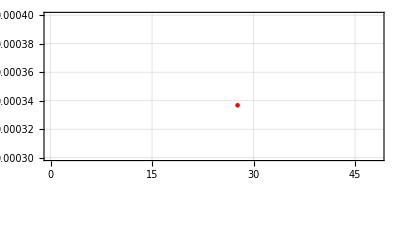

```mathematica
lstplt[1,1,1,Length[dat1]]
```

```mathematica
lstplt1[i1_,j1_,i2_,j2_]:=ListPlot[Table[{ex[prcs[[i2]]<>dat2[[j2]]][[k,Length[ex[prcs[[i2]]<>dat2[[j2]]][[1]]]]],ex[prcs[[i1]]<>dat1[[j1]]][[k,Length[ex[prcs[[i1]]<>dat1[[j1]]][[1]]]]]},{k,Length[ex[prcs[[i1]]<>dat1[[j1]]]]}],FrameLabel->{prcs[[i2]]<>dat2[[j2]],prcs[[i1]]<>dat1[[j1]]}]
(*Do[Print[lstplt[i1,j1,i2,j2]],{i1,Length[prcs]},{j1,Length[dat1]},{i2,Length[prcs]},{j2,j1+1,2+0Length[dat1]}]*)
```

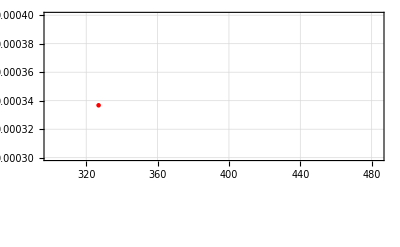

```mathematica
lstplt1[1,Length[dat1],1,Length[dat2]]
```

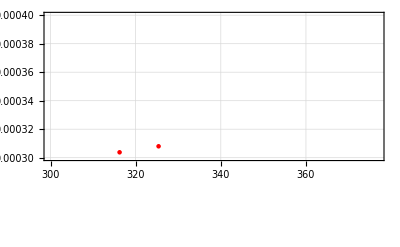

```mathematica
lstplt1[2,Length[dat1],2,Length[dat2]]
```

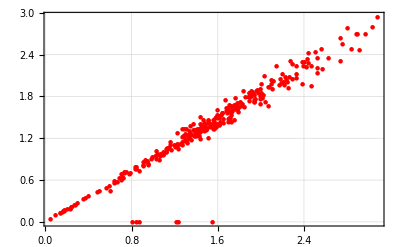

```mathematica
xsectionhhhzz=ListPlot[Table[{10^4 ex[prcs[[2]]<>dat1[[Length[dat1]]]][[k,Length[ex[prcs[[2]]<>dat1[[Length[dat1]]]][[Length[dat1]]]]]],10^4 ex[prcs[[1]]<>dat1[[Length[dat1]]]][[k,Length[ex[prcs[[1]]<>dat1[[Length[dat1]]]][[Length[dat1]]]]]]},{k,Length[ex[prcs[[2]]<>dat1[[Length[dat1]]]]]}],FrameLabel->{prcs[[2]]<>dat1[[Length[dat1]]]<>" (pb)",prcs[[1]]<>dat1[[Length[dat1]]]<>" (pb)"},PlotRange->All]
Export["/home/mashry/work/softleptogenesis/BL/draft/xsectionhhhzz.eps",xsectionhhhzz];
```

# ppzz4l

```mathematica
ppzz4ltxsection=ex[prcs[[2]]<>dat1[[Length[dat1]]]];
l1ppzz4lxsection=ex["l1"<>prcs[[2]]<>dat1[[Length[dat1]]]];
l2ppzz4lxsection=ex["l2"<>prcs[[2]]<>dat1[[Length[dat1]]]];
ppzz4ltxsection1=Table[ppzz4ltxsection[[i,l2ppzz4lxsection]],{i,l1ppzz4lxsection}];
Length[ppzz4ltxsection1]
```

16173

```mathematica
ppzz4lxsectionmaxpos=Ordering[ppzz4ltxsection1,-1]
ppzz4lxsectionmax=Extract[ppzz4ltxsection1,ppzz4lxsectionmaxpos]
(*Extract[thh2,ppzz4lxsectionmaxpos]*)
ppzz4ltxsection[[ppzz4lxsectionmaxpos]]
```

{16173}

0.000392507

{{126_11,0.000392507}}

```mathematica
thh2mdppzz4l=Import[path<>"ppzz4l_hh_2.dat"];
thh2ppzz4l=Table[thh2mdppzz4l[[2i-1]],{i,Ceiling[Length[thh2mdppzz4l]/2]}];
thh2dppzz4l=Table[thh2mdppzz4l[[2i]],{i,0,Ceiling[Length[thh2mdppzz4l]/2]}];
l1hh2ppzz4l=Length[thh2ppzz4l];
l2hh2ppzz4l=Length[thh2ppzz4l[[1]]];
thh2ppzz4l[[ppzz4lxsectionmaxpos]]
```

{{126_11,35,326.777}}

```mathematica
ppzz4lHS1=ex[prcs[[1]]<>dat1[[Length[dat1]-1]]];
l1ppzz4lHS1=ex["l1"<>prcs[[2]]<>dat1[[Length[dat1]-1]]];
l2ppzz4lHS1=ex["l2"<>prcs[[2]]<>dat1[[Length[dat1]-1]]];
ppzz4lHS=Table[ppzz4lHS1[[i,l2ppzz4lHS1]],{i,l1ppzz4lHS1}];
ppzz4lHS2=Ordering[ppzz4lHS];
Length[ppzz4lHS]
```

16173

```mathematica
ppzz4lHB1=ex[prcs[[1]]<>dat1[[Length[dat1]-2]]];
l1ppzz4lHB1=ex["l1"<>prcs[[2]]<>dat1[[Length[dat1]-2]]];
l2ppzz4lHB1=ex["l2"<>prcs[[2]]<>dat1[[Length[dat1]-2]]];
ppzz4lHB=Table[ppzz4lHB1[[i,3]],{i,l1ppzz4lHB1}];
ppzz4lHB2=Ordering[ppzz4lHB];
Length[ppzz4lHB]
```

16173

```mathematica
ptppzz4l[i_,j_]:={Ordering[ppzz4ltxsection1,-i][[j]],300000Extract[ppzz4ltxsection1,Ordering[ppzz4ltxsection1,-i][[j]]],
ppzz4ltxsection[[Ordering[ppzz4ltxsection1,-i][[j]]]],Extract[thh2ppzz4l,Ordering[ppzz4ltxsection1,-i][[j]]],ppzz4lHS1[[Ordering[ppzz4ltxsection1,-i][[j]]]],ppzz4lHB1[[Ordering[ppzz4ltxsection1,-i][[j]]]]};
Do[Print[ptppzz4l[i,1]],{i,2}]
```

{16173,117.752,{126_11,0.000392507},{126_11,35,326.777},{105_332,10,108.344},{105_332,8,1}}

{1572,108.453,{80_356,0.00036151},{80_356,35,304.461},{58_357,10,100.368},{58_357,8,1}}

```mathematica
datazz1=Table[{thh2ppzz4l[[i, 3]],10^4*ppzz4ltxsection[[i, l2ppzz4lxsection]],ppzz4lHS1[[i, 3]]}, {i,  l1ppzz4lxsection}];
χn0=70;χn=100;xsecmin=2.;xsecmax=4.0;mhpmin=290;mhpmax=400;
datazz=Select[datazz1,#[[3]]≤χn&];
```

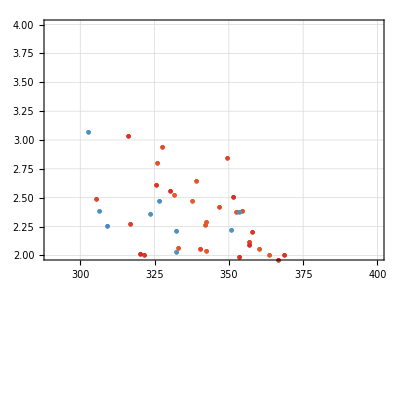
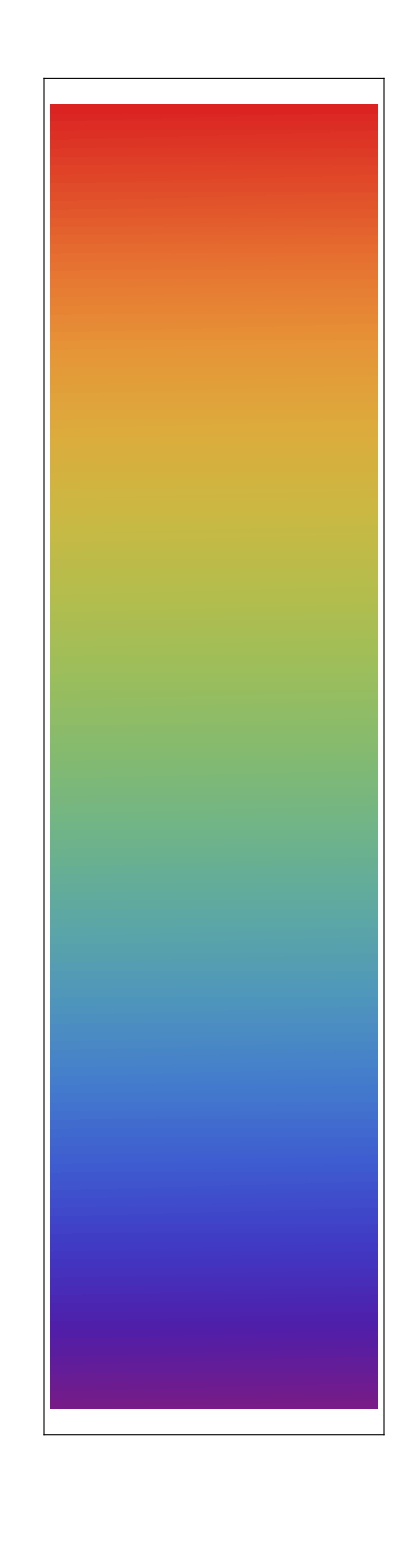

```mathematica
Clear[colorbar]
colorbar[{min_,max_},colorFunction_: Automatic,divs_: 150]:=DensityPlot[y,{x,0,0.1},{y,min,max},AspectRatio->10,PlotRangePadding->0,PlotPoints->{2,divs},MaxRecursion->0,Frame->True,FrameLabel->{{None,"χ^2"},{None,None}},RotateLabel->False,LabelStyle->Directive[FontFamily->"Helvetica",12],FrameTicks->{{None,All},{None,None}},FrameTicksStyle->Directive[FontFamily->"Helvetica",10,Plain],ColorFunction->colorFunction];
xsecmhpchi2zz=With[{opts={ImageSize->{Automatic,300}},cf="Rainbow"},Row[{ListPlot[List/@datazz[[All,{1,2}]],PlotStyle->({PointSize[0.01],ColorData[cf][#1]}&/@Rescale[datazz[[All,3]],{χn0,χn}]),PlotRange->{{mhpmin,mhpmax},{xsecmin,xsecmax}},AspectRatio->1,Frame->True,FrameLabel->{{"10^4×σ(pp->h'->ZZ->4l) (pb)",None},{"m_h' (GeV)",None}},Axes->None,FrameTicks->True,LabelStyle->Directive[FontFamily->"Helvetica",12],ImagePadding->{{50,10},{50,10}},opts],Show[colorbar[{χn0,χn},cf],ImagePadding->{{10,45},{50,10}},opts]}]]
Export["/home/mashry/work/softleptogenesis/BL/draft/xsecmhpchi2zz.eps",xsecmhpchi2zz];
```

# pphhaabb

```mathematica
pphhaabbtxsection=ex[prcs[[1]]<>dat1[[Length[dat1]]]];
l1pphhaabbxsection=ex["l1"<>prcs[[1]]<>dat1[[Length[dat1]]]];
l2pphhaabbxsection=ex["l2"<>prcs[[1]]<>dat1[[Length[dat1]]]];
pphhaabbtxsection1=Table[pphhaabbtxsection[[i,l2pphhaabbxsection]],{i,l1pphhaabbxsection}];
pphhaabbtxsection2=Ordering[pphhaabbtxsection1];
Length[pphhaabbtxsection1]
```

25877

```mathematica
pphhaabbxsectionmaxpos=Ordering[pphhaabbtxsection1,-1]
pphhaabbxsectionmax=Extract[pphhaabbtxsection1,pphhaabbxsectionmaxpos]
(*Extract[thh2,pphhaabbxsectionmaxpos]*)
pphhaabbtxsection[[pphhaabbxsectionmaxpos]]
```

{20567}

0.000349451

{{119_434,0.000349451}}

```mathematica
thh2mdpphhaabb=Import[path<>"pphhaabb_hh_2.dat"];
thh2pphhaabb=Table[thh2mdpphhaabb[[2i-1]],{i,Ceiling[Length[thh2mdpphhaabb]/2]}];
thh2dpphhaabb=Table[thh2mdpphhaabb[[2i]],{i,Ceiling[Length[thh2mdpphhaabb]/2]}];
l1hh2pphhaabb=Length[thh2pphhaabb];
l2hh2pphhaabb=Length[thh2pphhaabb[[1]]];
thh2pphhaabb[[pphhaabbxsectionmaxpos]]
```

{{119_434,35,331.18}}

```mathematica
pphhaabbHS1=ex[prcs[[1]]<>dat1[[Length[dat1]-1]]];
l1pphhaabbHS1=ex["l1"<>prcs[[1]]<>dat1[[Length[dat1]-1]]];
l2pphhaabbHS1=ex["l2"<>prcs[[1]]<>dat1[[Length[dat1]-1]]];
pphhaabbHS=Table[pphhaabbHS1[[i,l2pphhaabbHS1]],{i,l1pphhaabbHS1}];
pphhaabbHS2=Ordering[pphhaabbHS];
Length[pphhaabbHS]
```

25877

```mathematica
pphhaabbHB1=ex[prcs[[1]]<>dat1[[Length[dat1]-2]]];
l1pphhaabbHB1=ex["l1"<>prcs[[1]]<>dat1[[Length[dat1]-2]]];
l2pphhaabbHB1=ex["l2"<>prcs[[1]]<>dat1[[Length[dat1]-2]]];
pphhaabbHB=Table[pphhaabbHB1[[i,3]],{i,l1pphhaabbHB1}];
pphhaabbHB2=Ordering[pphhaabbHB];
Length[pphhaabbHB]
```

25877

```mathematica
(*Table[ex[prcs[[1]]<>"hh_2"][[2i-1]],{i,Ceiling[Length[ex[prcs[[1]]<>"hh_2"]]/2]}]*)
```

```mathematica
Ordering[pphhaabbtxsection1];
ptpphhaabb[i_,j_]:={Ordering[pphhaabbtxsection1,-i][[j]],300000Extract[pphhaabbtxsection1,Ordering[pphhaabbtxsection1,-i][[j]]],
pphhaabbtxsection[[Ordering[pphhaabbtxsection1,-i][[j]]]],(*Extract[thh2pphhaabb,Ordering[pphhaabbtxsection1,-i][[j]]],*)pphhaabbHS1[[Ordering[pphhaabbtxsection1,-i][[j]]]],pphhaabbHB1[[Ordering[pphhaabbtxsection1,-i][[j]]]]};
Do[Print[ptpphhaabb[i,1]],{i,5}]
```

{20567,104.835,{119_434,0.000349451},{119_434,10,142.65},{119_434,8,1}}

{18744,104.469,{115_321,0.000348229},{115_321,10,139.977},{115_321,8,1}}

{73,101.186,{54_72,0.000337287},{54_72,10,113.543},{54_72,8,1}}

{11951,101.155,{94_141,0.000337184},{94_141,10,116.714},{94_141,8,1}}

{13544,100.039,{97_396,0.000333462},{97_396,10,104.399},{97_396,8,1}}

```mathematica
(*ListPlot[Table[{i,Import[path<>"pphhaabb_xsection.dat"][[i,l2pphhaabbxsection]]},{i,l1pphhaabbxsection}]]*)
```

```mathematica
datahh1=Table[{thh2pphhaabb[[i, 3]],10^4*pphhaabbtxsection[[i, l2pphhaabbxsection]],pphhaabbHS1[[i, 3]]}, {i,  l1pphhaabbxsection}];
χn0=70;χn=100;xsecmin=2.;xsecmax=3.5;mhpmin=290;mhpmax=400;
datahh=Select[datahh1,#[[3]]≤χn&];
```

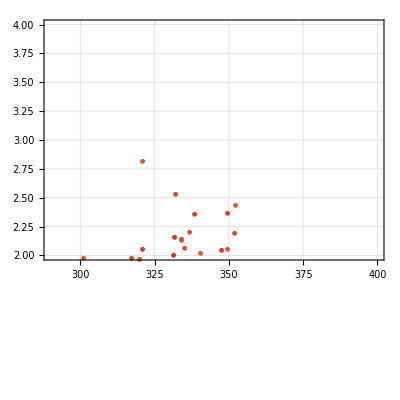
-Graphics--Graphics-

Export::nodir: Directory "/home/mashry/Dropbox/softleptogenesis/BL/draft/" does not exist.

Export::noopen: Cannot open "/home/mashry/Dropbox/softleptogenesis/BL/draft/xsecmhpchi2hh.eps".

```mathematica
Clear[colorbar]
colorbar[{min_,max_},colorFunction_: Automatic,divs_: 150]:=DensityPlot[y,{x,0,0.1},{y,min,max},AspectRatio->10,PlotRangePadding->0,PlotPoints->{2,divs},MaxRecursion->0,Frame->True,FrameLabel->{{None,"χ^2"},{None,None}},RotateLabel->False,LabelStyle->Directive[FontFamily->"Helvetica",12],FrameTicks->{{None,All},{None,None}},FrameTicksStyle->Directive[FontFamily->"Helvetica",10,Plain],ColorFunction->colorFunction];
xsecmhpchi2hh=With[{opts={ImageSize->{Automatic,300}},cf="Rainbow"},Row[{ListPlot[List/@datahh[[All,{1,2}]],PlotStyle->({PointSize[0.01],ColorData[cf][#1]}&/@Rescale[datahh[[All,3]],{χn0,χn}]),PlotRange->{{mhpmin,mhpmax},{xsecmin,xsecmax}},AspectRatio->1,Frame->True,FrameLabel->{{"10^4×σ(pp->h'->hh->bbγγ) (pb)",None},{"m_h' (GeV)",None}},Axes->None,FrameTicks->True,LabelStyle->Directive[FontFamily->"Helvetica",12],ImagePadding->{{50,10},{50,10}},opts],Show[colorbar[{χn0,χn},cf],ImagePadding->{{10,45},{50,10}},opts]}]]
Export["/home/mashry/Dropbox/softleptogenesis/BL/draft/xsecmhpchi2hh.eps",xsecmhpchi2hh];
Export["/home/mashry/work/softleptogenesis/BL/draft/xsecmhpchi2hh.eps",xsecmhpchi2hh];
```

# ppzz4lt-pphhaabb

```mathematica
ListPlot[List/@datahh1[[All,{1,2}]],PlotRange->{{mhpmin,mhpmax},{xsecmin,xsecmax}},FrameLabel->{{"10^4×σ(pp->h'->hh->bbγγ)",None},{"m_h'",None}},Axes->None,FrameTicks->True,LabelStyle->Directive[FontFamily->"Helvetica",12],ImagePadding->{{50,10},{50,10}}]
```

```mathematica
tgtpphhaabb=Import[path<>"pphhaabb_gYB.dat"];
l1gtpphhaabb=Length[thh2pphhaabb];
l2gtpphhaabb=Length[thh2pphhaabb[[1]]];
tgtpphhaabb[[pphhaabbxsectionmaxpos]]
```

{{119_434,10,-0.628133}}

```mathematica
datamhpgt1=Table[{tgtpphhaabb[[i, 3]],thh2pphhaabb[[i, 3]],pphhaabbHS1[[i, 3]]}, {i,  l1pphhaabbxsection}];
χn0=70;χn=100;gtmin=-1.;gtmax=.5;mhpmin=200;mhpmax=600;
datamhpgt=Select[datamhpgt1,#[[3]]≤χn&];
```

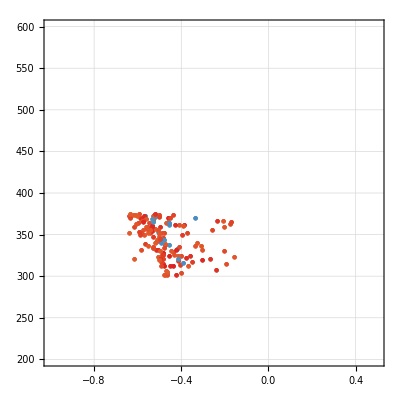
-Graphics--Graphics-

```mathematica
Clear[colorbar]
colorbar[{min_,max_},colorFunction_: Automatic,divs_: 150]:=DensityPlot[y,{x,0,0.1},{y,min,max},AspectRatio->10,PlotRangePadding->0,PlotPoints->{2,divs},MaxRecursion->0,Frame->True,FrameLabel->{{None,"χ^2"},{None,None}},RotateLabel->False,LabelStyle->Directive[FontFamily->"Helvetica",12],FrameTicks->{{None,All},{None,None}},FrameTicksStyle->Directive[FontFamily->"Helvetica",10,Plain],ColorFunction->colorFunction];
mhpgtchi2=With[{opts={ImageSize->{Automatic,300}},cf="Rainbow"},Row[{ListPlot[List/@datamhpgt[[All,{1,2}]],PlotStyle->({PointSize[0.01],ColorData[cf][#1]}&/@Rescale[datamhpgt[[All,3]],{χn0,χn}]),PlotRange->{{gtmin,gtmax},{mhpmin,mhpmax}},AspectRatio->1,Frame->True,FrameLabel->{{"m_h' (GeV)",None},{"gt",None}},Axes->None,FrameTicks->True,LabelStyle->Directive[FontFamily->"Helvetica",12],ImagePadding->{{50,10},{50,10}},opts],Show[colorbar[{χn0,χn},cf],ImagePadding->{{10,45},{50,10}},opts]}]]
Export["/home/mashry/work/softleptogenesis/BL/draft/mhpgtchi2.eps",mhpgtchi2];
```

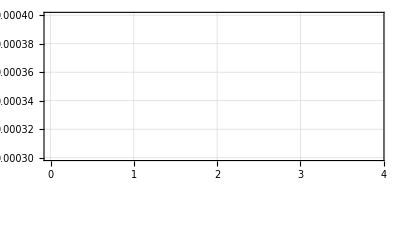

```mathematica
xsectionhhzz=ListPlot[Table[{10^4*ppzz4ltxsection[[i, l2ppzz4lxsection]],10^4*pphhaabbtxsection[[i, l2pphhaabbxsection]]}, {i,  l1ppzz4lxsection}],Frame->True,FrameLabel->{{"10^4×σ(pp->h'->ZZ->4l) (pb)",None},{"10^4×σ(pp->h'->hh->bbγγ) (pb)",None}},Axes->None,FrameTicks->True]
```